```mathematica
dataRaw=Import["C:\\Users\\juhaszn\\Documents\\HAL\\stochasticVariability\\output\\2022-04-27_11-21-48\\dataLastTick.csv"];
```

```mathematica
data=Flatten[dataRaw];
```

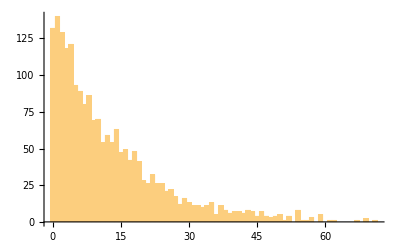

```mathematica
Histogram[data,Round[Max[data]]]
```

```mathematica
histogramList=HistogramList[data,Round[Max[data]]][[2]]
```

{132,140,129,118,121,93,89,80,86,69,70,54,59,54,63,47,49,42,48,41,28,26,32,26,26,21,22,17,12,16,13,11,11,10,11,13,5,11,8,6,7,7,6,8,7,4,7,4,3,4,5,1,4,0,8,1,1,3,0,5,0,1,1,0,0,0,0,1,0,2,0,1}

```mathematica
probabilities=histogramList/Length[data];
```

```mathematica
G[z_]:=Module[{},
sum=0;
For[i=1,i<=Length[histogramList],i++,
sum=sum+(Power[z,i-1])*probabilities[[i]]];
sum]
G[1.0]
```

1.

General::munfl: 0.0000204286^66 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^67 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

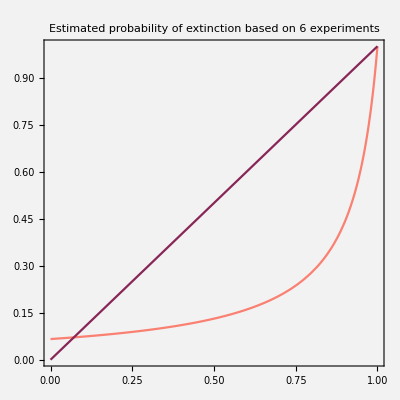

```mathematica
Plot[{G[z],z},{z,0,1},
AspectRatio->1,PlotRange->All,
PlotStyle->{ColorData["Legacy","Salmon"],ColorData["Legacy","Raspberry"]},
Frame->True,
PlotLabel->Style["Estimated probability of extinction based on 6 experiments",FontSize->12],
FrameStyle->Directive[ColorData["Legacy","SeaGreen"]],
Background->Lighter[Gray, 0.9]]
```